## 2 step with endosomes

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
ksyn = ki;
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
ki = kd1*γ;
kis = ki*β;
krec = τ*kd1;
kdeg = θ*kd1;
krecs = β2*krec;
```

### Equations 1

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12,e13,e14]
e1 =ksyn -k1*L1*r+kd1*b1+kd1*p1+kd1*q1-ki*r+krec*ri==0;(*R*)
e2 = ki*r-krec*ri-kdeg*ri==0;(*Ri*)
e3 = k1*L1*r-kd1*b1-kp*b1+kdp*p1-ki*b1+krec*b1i==0;(*B*)
e4 = ki*b1-krec*b1i-kdeg*b1i-kp*b1i+kdp*p1i==0;(*Bi*)
e5 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1-ki*p1+krec*p1i==0;(*P1*)
e6 = ki*p1-krec*p1i-kdeg*p1i+kp*b1i-kdp*p1i-kp*p1i+kdp*q1i==0;(*P1i*)
e7 = kp*p1-kdp*q1-kd1*q1-kis*q1+krecs*q1i==0;(*Q1*)
e8 = kp*p1i-kdp*q1i+kis*q1-krecs*q1i-kdeg*q1i==0;(*Q1i*)
solx1=Solve[{e1,e2,e3,e4,e5,e6,e7,e8},{r,b1,p1,q1,ri,b1i,p1i,q1i}][[1]];
r1 = ((p1+q1)/.solx1)/.{kd1->1,u1->u};
```

### Equations 2

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12,e13,e14]
(**)
e9 =ksyn -k2*L2*r+kd2*b2+kd2*p2+kd2*q2-ki*r+krec*ri==0;(*R*)
e10 = ki*r-krec*ri-kdeg*ri==0;(*Ri*)
e11 = k2*L2*r-kd2*b2-kp*b2+kdp*p2-ki*b2+krec*b2i==0;(*B*)
e12 = ki*b2-krec*b2i-kdeg*b2i-kp*b2i+kdp*p2i==0;(*Bi*)
e13 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2-ki*p2+krec*p2i==0;(*P1*)
e14 = ki*p2-krec*p2i-kdeg*p2i+kp*b2i-kdp*p2i-kp*p2i+kdp*q2i==0;(*P1i*)
e15 = kp*p2-kdp*q2-kd2*q2-kis*q2+krecs*q2i==0;(*Q1*)
e16 = kp*p2i-kdp*q2i+kis*q2-krecs*q2i-kdeg*q2i==0;(*Q1i*)
solx2=Solve[{e9,e10,e11,e12,e13,e14,e15,e16},{r,b2,p2,q2,ri,b2i,p2i,q2i}][[1]];
r2 = ((p2+q2)/.solx2)/.{kd1->1,u2->u};
```

## 2 step

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
ksyn = ki;
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
ki = kd1*γ;
kis = ki*β;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8]
e1 =ksyn -k1*L1*r+kd1*b1+kd1*p1+kd1*q1-ki*r==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1-ki*b1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1-ki*p1==0;(*P1*)
e4 = kp*p1-kdp*q1-kd1*q1-kis*q1==0;
(**)
e5 =ksyn -k2*L2*r+kd2*b2+kd2*p2+kd2*q2-ki*r==0;(*R*)
e6 = k2*L2*r-kd2*b2-kp*b2+kdp*p2-ki*b2==0;(*B1*)
e7 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2-ki*p2==0;(*P1*)
e8 = kp*p2-kdp*q2-kd2*q2-kis*q2==0;
```

### Solutions

```mathematica
Clear[ex2]
solx1=Solve[{e1,e2,e3,e4},{r,b1,p1,q1}][[1]];
r1 = ((p1+q1)/.solx1);
solx2=Solve[{e5,e6,e7,e8},{r,b2,p2,q2}][[1]];
r2 = ((p2+q2)/.solx2);
ex2[δ_,β_,γ_,ω_,ρ_]=FullSimplify[Limit[(r1/r2)/.{u1->u,u2->u},u->Infinity]]
```

((1+β γ+ω+ρ ω) ((γ+δ) (β γ+δ)+(γ ρ+2 δ (1+ρ)+β γ (2+ρ)) ω+(β+ρ+ρ^2) ω^2))/((β γ+δ+ω+ρ ω) ((1+γ) (1+β γ)+(2+(2+γ) ρ+β γ (2+ρ)) ω+(β+ρ+ρ^2) ω^2))

((1+β γ+ω) ((γ+δ) (β γ+δ)+2 (β γ+δ) ω+β ω^2))/((β γ+δ+ω) (1+β γ^2+ω (2+β ω)+γ (1+β+2 β ω)))

## Compare

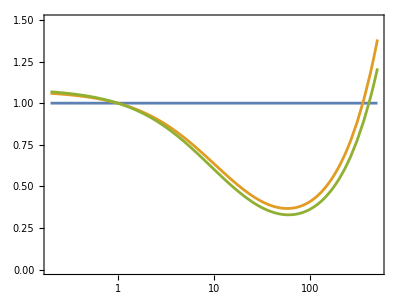

```mathematica
βE = 50;
γE = 0.05;
ωE = 10;
ρE = 0;
β2E = 0.5;
τE = 2*γE;
θE = 0.5*γE;
Show[LogLinearPlot[{1,ex2[δ,βE,γE,ωE,0],ex2i[δ,βE,β2E,γE,ωE,0,τE,θE,500]},{δ,1/5,500}],AspectRatio->0.75,TextStyle->FontSize->20,PlotRange->{0,1.5},Frame->True,Axes->False]
```